# LLM-Powered ML Pipeline Generator: Democratizing Advanced Machine Learning through Natural Language Interfaces

Image generated with Dall-e 3

Large Language Models (LLMs) excel at prediction and planning, making them powerful for programming tasks. However, they struggle with precise algorithm execution. This project leverages LLMs’ strengths to enhance Machine Learning (ML) model development and deployment. While LLMs can understand ML model architecture, they usually have a hard time at directly implementing them. Our approach enables LLMs to manipulate ML models, effectively combining the strengths of both technologies. By doing so, we create a powerful synergy that can tackle complex tasks which neither LLMs nor traditional ML models could solve independently.

## How does it works?

LLM-Powered ML Pipeline Generator consist of four parts: Task Creation, Document Retrieve, Tools Calling, and Content Generation.

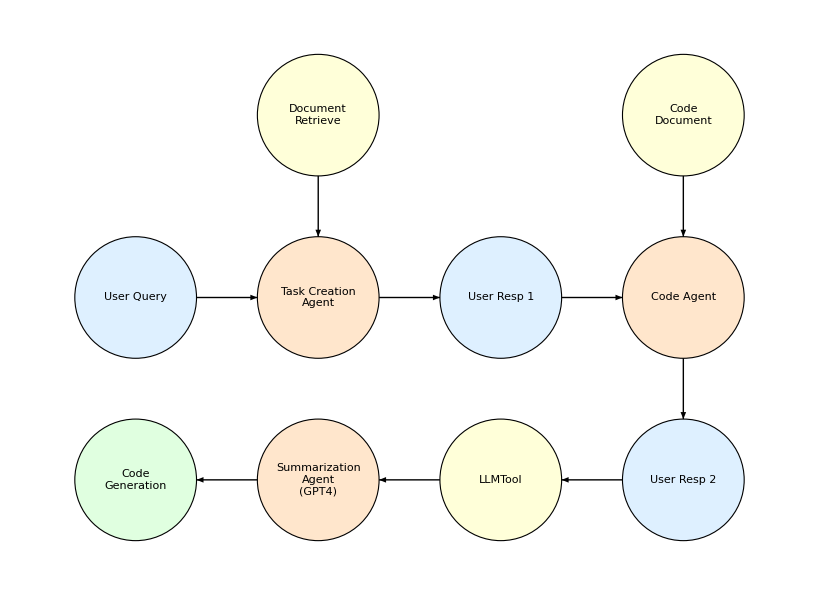

```mathematica
r=1; (*radius of each disk*)

(*center of each disk.Numbers left to right,top to bottom*)
c1={0,-(r+2)};c2={r+2,0};c3={r+5,-(r+2)};c4={r+2,-(r+2)};c5={0,-(r+5)};
c6={r+2,-(r+5)};
c7={r+8,-(r+2)};
c8={r+8,0};
c9={r+8,-(r+5)};
c10={r+5,-(r+5)};

makeDisk[r_,c_]:={EdgeForm[Black],LightYellow,Disk[c,r]}(*change as needed*)
makeDiskUser[r_,c_]:={EdgeForm[Black],LightBlue,Disk[c,r]}(*change as needed*)
makeDiskAgent[r_,c_]:={EdgeForm[Black],LightOrange,Disk[c,r]}(*change as needed*)
makeDiskDone[r_,c_]:={EdgeForm[Black],LightGreen,Disk[c,r]}(*change as needed*)

makeArrow[from_,to_,dir_]:=Module[{z=Cos[Pi/4]},
Which[
dir=="right",
Arrow[{{from[[1]]+r,from[[2]]},{to[[1]]-r,to[[2]]}}],

dir=="left",
Arrow[{{from[[1]]-r,from[[2]]},{to[[1]]+r,to[[2]]}}],

dir=="down",
Arrow[{{from[[1]],from[[2]]-r},{to[[1]],to[[2]]+r}}],

dir=="right-down",
Arrow[{{from[[1]]+z,from[[2]]-z},{to[[1]]-z,to[[2]]+z}}],

dir=="left-down",
Arrow[{{from[[1]]-z,from[[2]]-z},{to[[1]]+z,to[[2]]+z}}]
]
];

putLabel[txt_,at_]:=Style[Text[txt,at],Bold,12]
Graphics[{makeDiskUser[1,c1],
makeDisk[1,c2],
makeDiskUser[1,c3],
makeDiskAgent[1,c4],
makeDiskDone[1,c5],
makeDiskAgent[1,c6],
makeDiskAgent[1,c7],
makeDisk[1,c8],
makeDiskUser[1,c9],
makeDisk[1,c10],
makeArrow[c2,c4,"down"],
makeArrow[c6,c5,"left"],
makeArrow[c1,c4,"right"],
makeArrow[c4,c3,"right"],
makeArrow[c3,c7,"right"],
makeArrow[c8,c7,"down"],
makeArrow[c7,c9,"down"],
makeArrow[c9, c10, "left"],
makeArrow[c10,c6,"left"],
putLabel["User Query",c1],
putLabel["Document\nRetrieve",c2],
putLabel["User Resp 1",c3],
putLabel["Task Creation\nAgent",c4],
putLabel["Code\nGeneration",c5],
putLabel["Summarization\nAgent\n(GPT4)",c6],
putLabel["Code Agent",c7],
putLabel["Code\nDocument",c8],
putLabel["User Resp 2",c9],
putLabel["LLMTool",c10]
},
Axes->False]
```

This pip-line can build a ML tool in three rounds conversion. We can roughly break it into three stages: ML Model Selection, Code Generation and LLMTool Calling.

## ML Model Selection

## Prompting User Question

We need to identify the user’s question to decide which model is the best option to start. We are using web scarping to get Wolfram Neural Net Repository  model information.

First, we want to handle user’s question then let Task Creation Agent to search the best top 3 ML models for this work.

```mathematica
question = "GGiven an image and multiple text descriptions, find the text that better describes the image";

promptTemplate = StringTemplate[
	StringJoin[
		"# You are an expert on Machine Learning and Deep Learning.",
		"\n\n",
		"## Your main task is choose best model for user's task",
		"\n\n",
		"Here are top three infomation about ML models that closed to user's case,
 you have to read it first. Then you will choose the best fit 
model my case if there is not best fit for user request you need 
to find close one with explanation why you choose it. Your must explain why this model 
is good for user case.",
		"\n\n",
		"### Models Info\n",
		"~~~~~~\nStart of Search Results\n~~~~~~\n`modelRetrieve`\n~~~~~~\nEnd of of Search Result\n~~~~~~",
		"\n\n",
		"## User's Request\n",

		"~~~~~~\nStart of User's Query\n~~~~~~\n`userQuery`\n~~~~~~\nEnd of of User's Query\n~~~~~~"
]]
```

TemplateObject[…]

## Create a RAG system (Optional)

We have two RAG systems to build in this pipeline. They are Model Description Doc and Model Documentation Doc:

Model Description Document: Web scraping from Wolfram Neural Network List, which contains pure text information about available models. Each embedding cell is each single model info. This is for Task Creation Agent to select the best fit for user’s task.

Model Documentation Document: Documentation of each model details, which is consist of code example that LLM can directly use and text description of this model. Each embedding cell is each single model info. This is for Code Generation Agent to retrieve the document of choosing model.

### Model Description Document RAG

```mathematica
mdContent = ;
sections = StringSplit[mdContent,"---"];
processedSections=StringTrim/@sections;
Length[processedSections]

(*Get access to OpenAI's embedding model*)
(*This is the optional! Only use for the first time embeding*)
(*embeddings = Map[ServiceExecute["OpenAI", "Embedding", {"Input" -> #, "Model" -> "text-embedding-3-small"}]&,processedSections];*)
(*Export the embedding model*)
(*Export["/Users/tzz/Documents/WSS2024/wss24_project_embeddings.wl",embeddings]*)

(*This is importing embedded model*)
embeddings=;

embeddingsToText = MapThread[Rule[#1,#2]&,{embeddings[[All,"data",1,"embedding"]],processedSections}];

nfunction = Nearest[embeddingsToText, DistanceFunction->CosineDistance];

getEmbedding[text_String]:=
ServiceExecute[
"OpenAI",
"Embedding",
{
"Input" -> text, 
"Model" -> "text-embedding-3-small"
}
][["data",1,"embedding"]];
```

158

Check if the function work

```mathematica
(*Function for calling retrieve info*)
nfunction[getEmbedding["CLIP image and text pair or descrption"],1]
```

{### Model Name

Name: "BLIP Image-Text Matching Nets Trained on Captioning Datasets"

### Description of the model

Bootstrapping Language- Image Pre-training(BLIP) model support multimodel encoder which is the best choice for image-text task. It has way much better accurate rate for pairing image and text than regular imagenocder and textencoder(eg, CLIP). BLIP is advanced the performance for many vision-language tasks. Suppose you have a databese where are stored thousands of images and you want to find just one of them. The BLIP the best choice until July 5, 2024

### Trained by Data

DataSet: "Captioning Datasets"

### Time issued

July 5, 2024}

### Model Documentation Document RAG

```mathematica
mdContent = ;
sectionsDoc = StringSplit[mdContent,"---"];
processedSectionsDoc=StringTrim/@sectionsDoc;
Length[processedSectionsDoc]

(*Get access to OpenAI's embedding model*)
(*This is the optional! Only use for the first time embeding*)
(*embeddingsDoc = Map[ServiceExecute["OpenAI", "Embedding", {"Input" -> #, "Model" -> "text-embedding-3-small"}]&,processedSectionsDoc];*)
(*Export the embedding model*)
(*Export["/Users/tzz/Documents/WSS2024/wss24_project_embeddingsDoc.wl",embeddings]*)

(*This is importing embedded model*)
embeddingsDoc=;

embeddingsToTextDoc = MapThread[Rule[#1,#2]&,{embeddingsDoc[[All,"data",1,"embedding"]],processedSectionsDoc}];

nfunctionDoc = Nearest[embeddingsToTextDoc, DistanceFunction->CosineDistance];

getEmbedding[text_String]:=
ServiceExecute[
"OpenAI",
"Embedding",
{
"Input" -> text, 
"Model" -> "text-embedding-3-small"
}
][["data",1,"embedding"]];
```

3

Check if the function work

```mathematica
(*Function for calling retrieve info*)
nfunctionDoc[getEmbedding["BLIP image and text pair or descrption"],1]
```

{# Tool Name: BLIP Image-Text Matching Nets Trained on Captioning Datasets

## Tool Description
This tool is called `LLMResourceTool["ImageSearcher"]` you can directly follow the code example below to use it. It is aimed for matches a product image with the most relevant description from a provided dataset using a multimodalEncoder model. It's specifically designed for products like lamps and chairs. The tool requires an image dataset, a description dataset, a product image, and a text description as inputs. It outputs the best matching description for the given product image.

This tool is using `BLIP Image-Text Matching Nets Trained on Captioning Datasets` model.

Usage Instructions for LLM:

Input: `descriptionFile` the absolute path to the `csv` file; `imageFolder` the absolute path to the images folder; `targetImageAssociation` association of the images user wants to send.

Output: The closest text description of the image user sent.

This is for image input then get text output only.

## How to use it

Initialize the tool. You can simply call the tool name like here to import this tool

```wolfram
(*First load this tool*)
toolLoad = LLMResourceTool["ImageSearcher"];

(*set up the parameters*)
tool = toolLoad[<|
   "descriptionFile" -> descriptionFile, (*replace the descriptionFile with the path to the description file*)
   "imageFolder" -> imageFolder, (*replace the imageFolder with the path to the image folder*)
   "targetImageAssociation" -> targetImageAssociation (*replace the targetImageAssociation with the target image association*)
    |>]
```

You have to make sure you have `descriptionFile`, `imageFolder` and `targetImageAssociation` defined already. 

Now you can use below code for the most similar text:

```wolfram
(*Example User query*)
userQuery2 = "The \"testImage\" is the one you need to find descrption for me. Organize this item infomation for me";

(*Connect LLM with the tool and do the search*)
LLMSynthesize[userQuery2,
	LLMEvaluator -> <|
		"Tools"-> tool
		|>]
```

That’s it. That is all the code you need to use the tool.}

## Task Creation Agent Respond

Then, the Task Creation Agent will use Retrieval-Augmented Generation(RAG) that we defined to filter the best model for us.

First set up the template and LLM status with LLMFunction:

```mathematica
llmSteup = LLMFunction[
  promptTemplate, (* Specify the prompt template to use. *)
  LLMEvaluator -> <|
    "Model" -> {"OpenAI","gpt-4o"}, (* Specify the model to use for LLM evaluation. *)
    "Temperature" -> 0.5 (* Set the temperature parameter for deterministic outputs. *)
  |>
];
```

Now, we will send user’s first query to the Model Description Doc RAG to get the best three option models

```mathematica
retrieveModel = nfunction[getEmbedding[question],3]; (*Get retrieve results*)

(*Generate first respond from Agent*)
firstOutput = llmSteup[<|
"modelRetrieve" -> retrieveModel,
"userQuery" -> question
|>];
```

```mathematica
firstOutput
```

Based on the user's request, they need a model that can take an image and multiple text descriptions and find the text that best describes the image. This task falls under the category of image-text matching, which involves pairing an image with its most relevant text description. 

Among the models listed:

1. **Wolfram ImageIdentify Net V1**: This model is designed to identify the main object in an image. It does not handle text descriptions or matching images to text.

2. **BLIP Image-Text Matching Nets Trained on Captioning Datasets**: This model is specifically designed for image-text matching tasks. It uses a multimodal encoder to pair images and text, and it has been noted to have a better accuracy rate for this task compared to other models like CLIP. This model is advanced for many vision-language tasks and is explicitly mentioned as the best choice for tasks involving finding a specific image from a database based on text descriptions.

3. **Ademxapp Model A**: Similar to the Wolfram ImageIdentify Net V1, this model focuses on identifying the main object in an image and does not handle text descriptions or matching images to text.

Given the user's requirement to match an image with the best-fitting text description, the **BLIP Image-Text Matching Nets Trained on Captioning Datasets** is the most suitable model. This model is designed precisely for the task of matching images with text descriptions and has been noted for its superior performance in this domain.

### Why BLIP is the best fit:
- **Task Alignment**: BLIP is designed for image-text matching tasks, which aligns perfectly with the user's request.
- **Performance**: It has a higher accuracy rate for pairing images and text than other models like CLIP.
- **Advanced Capabilities**: BLIP advances performance in many vision-language tasks, making it a robust choice for the user's needs.

Therefore, the BLIP Image-Text Matching Nets Trained on Captioning Datasets is the best fit for the user's query.

Great! It looks like LLM choose the best fitting model for us from the three models that from our model database.

#### Note for Readers

To save on token costs, our pipeline will not pass every single output from the LLM to the next step, but it will still function normally and handle everything effectively.

## Code Generation

After we get the agent’s response, we will know the best ML model for our task. The next step the user needs to do is to confirm if this is the model they want to use. Then, we will start to get the target model’s documentation and generate the appropriate code to get it ready to run.

## Model Document Retrieve

After get respond from Task Creation Agent, user can authorize LLM to use this model for their task

```mathematica
userRespond = "let's use BLIP Image-Text Matching Nets"; (*User's confirmation*)
```

### Create a new prompt template for Code generation

```mathematica
codePromptTemplate = StringTemplate[
	StringJoin[
		"# You are an expert on coding wolfram language",
		"\n\n",
		"## Your main task is to write the  read the \"Tool Documentation\" on and then write the Wolfram Language code within it (Write only code).",
		"\n\n",
		"Once you get the user's request and retrieved document, check if they are same model: if yes,
then staring read the 'How to use it' section and learn how to use the tool . If no, then ask user if the model document 
match the model he chose. IMPORTANT! you will just use the code under 'How to use it' you cannot change
the code just directly use it.",
		"\n\n",
		"### Tool Documentation\n",
		"~~~~~~\nStart of Documentation\n~~~~~~\n`modelDoc`\n~~~~~~\nEnd of of Documentation\n~~~~~~",
		"\n\n",
		"## User's Respond\n",

		"~~~~~~\nStart of User's Respond\n~~~~~~\n`userRespond`\n~~~~~~\nEnd of of User's Respond\n~~~~~~"
]];
```

Now let’s setup this document agent to work

```mathematica
(*Check your version first! You have to get at least v14.1 to make it work*)
llmDocSteup = LLMFunction[
  codePromptTemplate, (* Specify the prompt template to use. *)
  LLMEvaluator -> <|
    "Model" -> {"OpenAI","gpt-4o"}, (* Specify the model to use for LLM evaluation. *)
    "Temperature" -> 0 (* Set the temperature parameter for deterministic outputs. *)
  |>
];
```

NOTE: If your Mathematica is 14.0 and under it, the LLMFunction will not work for sending code snippet. We have to custom a new function to make it work.

```mathematica
(*If you are under v14.1 please use this function*)
customLLMFunction[prompt_]:=ServiceExecute["OpenAI","Chat",
	{"Messages"->{
		<|"Role"->"User","Content"->{prompt}|>},
		"Model"->"gpt-4o-2024-05-13"}
		][[1,"message","content"]];
```

Now we are ready to get the model document from Document RAG

For v14.1 +

```mathematica
retrieveDoc = nfunctionDoc[getEmbedding[userRespond],1];

secondOutput = llmDocSteup[<|
	"modelDoc" -> retrieveDoc,
	"userRespond" -> userRespond
|>];
```

For under v14.1

```mathematica
retrieveDoc = nfunctionDoc[getEmbedding[userRespond],1];
ClearAll[secondOutput]
secondOutput = customLLMFunction[codePromptTemplate[<|
	"modelDoc" -> retrieveDoc,
	"userRespond" -> userRespond
|>]];
```

```mathematica
secondOutput
```

```wolfram
(*First load this tool*)
toolLoad = LLMResourceTool["ImageSearcher"];

(*set up the parameters*)
tool = toolLoad[<|
   "descriptionFile" -> descriptionFile, (*replace the descriptionFile with the path to the description file*)
   "imageFolder" -> imageFolder, (*replace the imageFolder with the path to the image folder*)
   "targetImageAssociation" -> targetImageAssociation (*replace the targetImageAssociation with the target image association*)
    |>]

(*Example User query*)
userQuery2 = "The \"testImage\" is the one you need to find descrption for me. Organize this item infomation for me";

(*Connect LLM with the tool and do the search*)
LLMSynthesize[userQuery2,
	LLMEvaluator -> <|
		"Tools"-> tool
		|>]
```

Now we get the code that ready to work. The last thing is simply provide the dataset user has and run it.

## LLMTool Calling

In this step, we will build a simple prompt template to GPT-4 so that it will make sure calling the LLMTool correctly with user’s input.

```mathematica
ToolPromptTemplate = StringTemplate[
	StringJoin[
		"# You are an expert on coding wolfram language",
		"\n\n",
		"## Your main task is to add \"User's Dataset\" and \"User's Query\" into \"Tool Code Example\" appropriately make sure it can run write then 
return the Wolfram Language code within it (Write only code).",
		"\n\n",
		"Once you get \"Tool Code Example\", \"User's Dataset\" and \"User's Query\", you need to understand the which part of the Tool code example 
need to replace, then find them in \"User's Dataset\" and \"User's Query\". If you think user's input is not enough, 
you need to return the message ask user to provide.",
		"\n\n",
		"## Tool Code Example\n",
		"~~~~~~\nStart of Tool Code Example\n~~~~~~\n`toolCode`\n~~~~~~\nEnd of Tool Code Example\n~~~~~~",
		"\n\n",
		"## User's Dataset\n",
		"~~~~~~\nStart of User's Dataset\n~~~~~~\n`userDataset`\n~~~~~~\nEnd of of User's Dataset\n~~~~~~",
		"\n\n",
		"## User's Query\n",
		"~~~~~~\nStart of User's Query\n~~~~~~\n`userQuery`\n~~~~~~\nEnd of of User's Query\n~~~~~~"
]];
```

Until this step, we are ready to accept user’s dataset and task request!

```mathematica
(*User's Dataset*)
descriptionFile="/Users/tzz/Documents/WSS2024/LampDS_WSS_Up2.csv";
imageFolder="/Users/tzz/Documents/WSS2024/Products/sample";
targetImageAssociation =<|"testImage"->-Graphics-,"testImage2"->-Graphics-|>;
(*User's Query*)
userRequest = "The \"testImage\" is the one you need to find descrption for me. Organize this item infomation for me";
```

Here we pack up the description, images, and target Image into User’s Data

```mathematica
PrintVariables[] := Module[{},
  <|"Description Data: descriptionFile" -> descriptionFile, 
    "Images Data: imageFolder" -> imageFolder, 
    "Target Image Association: targetImageAssociation" -> "targetImageAssociation"|>
]

userDataSet = PrintVariables[]
```

<|Description Data: descriptionFile→/Users/tzz/Documents/WSS2024/LampDS_WSS_Up2.csv,Images Data: imageFolder→/Users/tzz/Documents/WSS2024/Products/sample,Target Image Association: targetImageAssociation→targetImageAssociation|>

```mathematica
ConentOutput = customLLMFunction[ToolPromptTemplate[<|
	"toolCode" -> secondOutput,
	"userDataset" -> userDataSet,
	"userQuery" -> userRequest
|>]];
```

```mathematica
ConentOutput
```

```wolfram
(*First load this tool*)
toolLoad = LLMResourceTool["ImageSearcher"];

(*set up the parameters*)
tool = toolLoad[<|
   "descriptionFile" -> "/Users/tzz/Documents/WSS2024/LampDS_WSS_Up2.csv", (*path to the description file*)
   "imageFolder" -> "/Users/tzz/Documents/WSS2024/Products/sample", (*path to the image folder*)
   "targetImageAssociation" -> targetImageAssociation (*replace the targetImageAssociation with the target image association*)
    |>]

(*User query*)
userQuery2 = "The \"testImage\" is the one you need to find descrption for me. Organize this item infomation for me";

(*Connect LLM with the tool and do the search*)
LLMSynthesize[userQuery2,
	LLMEvaluator -> <|
		"Tools"-> tool
		|>]
```

Now we got the the code ready to run! Let’s run it!

```mathematica
extractCode[result_String]:=First@StringCases[result,"```wolfram\n"~~code__~~"\n```"->code]

ToExpression[extractCode[ConentOutput]]
```

Sure, I'll find the best matching description for the "testImage" in the provided dataset. I'll proceed to match the image and retrieve the relevant product information.

Let's begin by calling the tool to match the "testImage" with the description dataset.

```json
Here is the organized information for the item "B9588-2" lamp:

### Product Description
**B9588-2 Lamp**

### Key Characteristics:
1. **Flower Bulb**:
   - Top flower-like glass bulb with a golden hue.
2. **Central Disc**:
   - Textured, translucent circular disc with a golden core.
3. **Orbits and Star**:
   - Two thin golden orbits with a small star.
4. **Base**:
   - Simple circular golden wall mount.
5. **Lighting**:
   - Warm ambient light, both direct and diffused.

### Summary:
The B9588-2 lamp features a unique and elegant design with celestial elements. It combines decorative and functional aspects with a flower-like glass bulb, a textured central disc, ornate orbits, and a star, all accentuated by a golden finish. The lighting provided is warm and ambient, suitable for creating cozy atmospheres.

This should include all relevant details about the "B9588-2" lamp. If you need any more information or assistance, feel free to ask!

Boom! That our result!

## Calling Model’s LLMTool Manually (optional)

Calling the target tool

```mathematica
(*define the source data*)
descriptionFile="/Users/tzz/Documents/WSS2024/LampDS_WSS_Up2.csv";
imageFolder="/Users/tzz/Documents/WSS2024/Products/sample";
targetImageAssociation =<|"testImage"->-Graphics-,"testImage2"->-Graphics-|>;
```

```mathematica
toolLoad = LLMResourceTool["ImageSearcher"];

tool= toolLoad[
	<|"descriptionFile"->descriptionFile, 
	"imageFolder"->imageFolder, 
	"targetImageAssociation"-> targetImageAssociation
	|>]
```

LLMTool[<|Name -> ImageSearcher, Description -> This tool matches a product image with the m<<300>>the given product image., <<1>>, Function -> (LLMToolRepositoryTemporary`processMultimodalData[/Users/tzz/Documents/WSS2024/LampDS_WSS_Up2.csv, /Users/tzz/Documents/WSS2024/Products/sample, Association[{testImage -> -Image-, testImage2 -> -Image-}][#targetImageName]] & )|>, {}]

                                                Usage Instructions for LLM:
                                                1. Initialize the tool: Provide the imageDat<<94>>l will use for matching.
                                                2. Upload an image and provide a description<<132>>to match with the image.
                                                3. Call the match function: Use the match fu<<123>>and find the best match.
                                                4. Retrieve the output: The tool will return<<58>> for the uploaded image.

                                                The images you can use are: {testImage, testImage2}

```mathematica
userQuery2 = "The \"testImage\" is the one you need to find descrption for me. Organize this item infomation for me";


LLMSynthesize[userQuery2,
	LLMEvaluator-><|
		"Tools"-> tool
		|>]
```

Sure, I can help with that. I'll start by initializing the tool with the provided image and description datasets. Then I'll upload the "testImage" and find the best matching description for it.

Let's begin with finding the appropriate description for the "testImage".



Here's the organized information for the item you've inquired about:

**Product Name**: B9588-2 Lamp

**Description**:
The B9588-2 lamp features a striking golden metallic structure adorned with celestial elements, making it a beautiful and eye-catching piece for any space. Here are its key characteristics:

1. **Flower Bulb**: 
   - Top flower-like glass bulb
   - Golden hue
   
2. **Central Disc**: 
   - Textured and translucent circular disc
   - Golden core

3. **Orbits and Star**: 
   - Two thin golden orbits
   - Small star integrated within the orbits
   
4. **Base**: 
   - Simple circular golden wall mount
   
5. **Lighting**: 
   - Warm ambient light
   - Provides both direct and diffused lighting

This lamp brings together a blend of delicate artistry and functional brilliance, making it a perfect addition to illuminate and enhance the aesthetic appeal of your home or office space.